```mathematica
<<Radia`;
```

Radia Version: 4.32 is loaded

Radia is copyright ESRF, France.

Portions copyright Synchrotron SOLEIL, France.

Portions copyright Wolfram Research, Inc.

```mathematica
magR = 0.005;
magH = 0.01;
magM = {0,0,1};
K = 12;
dX = 0.01;
R = 0.06;
```

```mathematica
radObjCylin[R_,H_,M_,K_,x0_,y0_,z0_]:=Module[{x,y,z,points,face,g},
	x = Table[R*N[Cos[2 Pi/K k]], {k, 0, K-1}];
	y = Table[R*N[Sin[2 Pi/K k]], {k, 0, K-1}];
	z = Table[H/2, {k, 0, K-1}];
	points = Transpose[{Join[x+x0,x+x0],Join[y+y0,y+y0],Join[-z+z0,z+z0]}];
	face = {Range[1,K]};
	AppendTo[face,Range[1,K]+K];
	For [k=1, k<=K-1, k++,AppendTo[face,{k,k+1,k+1+K,k+K}]];
	AppendTo[face,{K,1,1+K,K+K}];
	g = radObjPolyhdr[points,face,{0,0,1}]
];
```

```mathematica
g = radObjCylin[0.06,0.005,{0,0,0},24,0,0,0];
For[nx=-20, nx<=20, nx++,
	For[ny=-20, ny<=20, ny++,
		x = nx*dX + Mod[ny,2]*dX/2;
		y = ny*dX*Sqrt[3]/2;
		z = 0.01;
		If[(x^2+y^2)<R^2,g=radObjCnt[{g,radObjCylin[magR,magH,magM,K,x,y,z]}];];
	]
]
draw=radObjDrw[g];
RadPlot3DOptions[];
Show[Graphics3D[draw], ViewPoint->{5,-1.5,1}, PlotRange->All, AmbientLight->GrayLevel[0.1], AspectRatio->1]
```

-Graphics3D-

```mathematica
g = radObjCylin[0.06,0.01,{0,0,0},K,0,0,0];
draw=radObjDrw[g];
RadPlot3DOptions[];
Show[Graphics3D[draw], ViewPoint->{5,-1.5,1}, PlotRange->All, AmbientLight->GrayLevel[0.1],]
```

-Graphics3D-

```mathematica
radObjCylin[R_,H_,M_,K_,x0_,y0_,z0_]:=Module[{x,y,z,points,face},
	x = Table[magR*N[Cos[2 Pi/K k]], {k, 0, K-1}];
	y = Table[magR*N[Sin[2 Pi/K k]], {k, 0, K-1}];
	z = Table[magH/2, {k, 0, K-1}];
	points = Transpose[{Join[x+x0,x+x0],Join[y+y0,y+y0],Join[-z+z0,z+z0]}];
	face = {Range[1,K]};
	AppendTo[face,Range[1,K]+K];
	For [k=1, k<=K-1, k++,AppendTo[face,{k,k+1,k+1+K,k+K}]];
	AppendTo[face,{K,1,1+K,K+K}];
	g = radObjPolyhdr[points,face,{0,0,1}]
];
```

```mathematica
g = radObjCylin[magR,magH,magM,K,1,0,0];
draw=radObjDrw[g];
RadPlot3DOptions[];
Show[Graphics3D[draw], ViewPoint->{5,-1.5,1}, PlotRange->All, AmbientLight->GrayLevel[0.1]]
```

-Graphics3D-

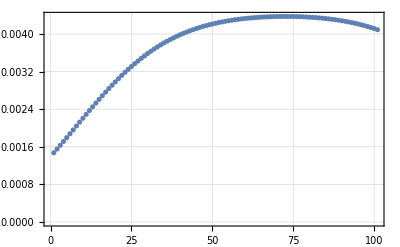

```mathematica
RadPlotOptions[];
Bz=radFldLst[M,"bz",{0,5,5},{10,5,5},101, "noarg"];
ListPlot[Bz]
```